```mathematica
(* For E in eV between 1 and 10000 eV above the Fermi Level.
a is the monolayer thickness in nanometers *)

elements[E_,a_]:=538/E^2*a+.41(a*E)^(1/2)*a;
inorganic[E_,a_]:=2170/E^2*a+0.72(a*E)^(1/2)*a;(* mean free path in monolayers *)
organic[E_,a_]:=49/E^2+0.11(a*E)^(1/2); (* The mean free path? in mg m^-2*)
aGraphene=.335; (*nm*)
```

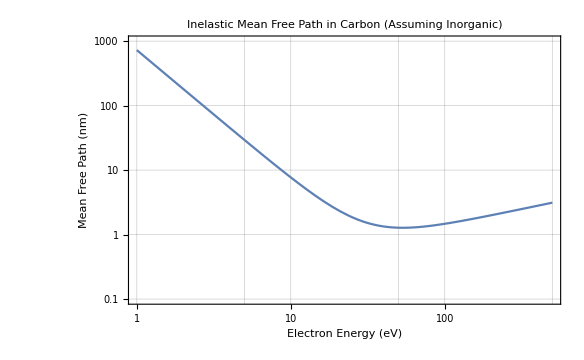

```mathematica
LogLogPlot[inorganic[energy,aGraphene],{energy,1,500},PlotRange->{.1,1000},Frame->True,GridLines->Automatic,LabelStyle->20,FrameLabel->{"Electron Energy (eV)","Mean Free Path (nm)"},PlotLabel->"Inelastic Mean Free Path in Carbon (Assuming Inorganic)"]
```

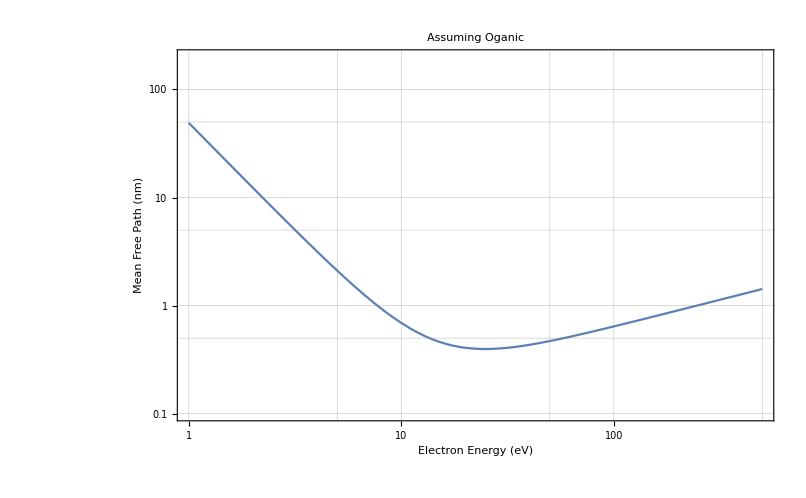

```mathematica
LogLogPlot[organic[energy,aGraphene],{energy,1,500},PlotRange->{.1,200},Frame->True,GridLines->Automatic,LabelStyle->20,PlotLabel->"Assuming Oganic",FrameLabel->{"Electron Energy (eV)","Mean Free Path (nm)"}]
```

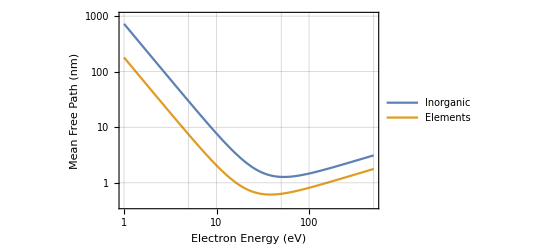

```mathematica
plot=LogLogPlot[{inorganic[energy,aGraphene],elements[energy,aGraphene]},{energy,1,500},PlotRange->{.4,1000},Frame->True,GridLines->Automatic,FrameLabel->{"Electron Energy (eV)","Mean Free Path (nm)"},PlotLegends->{"Inorganic","Elements"},ImageSize->{Automatic,UpTo[2*72]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["electronsThroughSolids.png",plot,ImageResolution->200]
ResetDirectory[]
```

C:\Users\kahrendsen2\Box Sync\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\theory

electronsThroughSolids.png

C:\Users\kahrendsen2\Documents